```mathematica
r=3.6;
L=0.5;
σ=Log[4/r]*√(2/3)*Tanh[L/4]/(√Tanh[L/2])
α=σ^2*Tanh[L/2]
```

0.0216161

0.00011444

```mathematica
Cor[x_,L_]:=((Exp[2L]-1)/(Exp[2L]-2Cos[2π*x]*Exp[L]+1))*α
```

```mathematica
S[n_,L_]:=α*Exp[-L*Abs[n]]
```

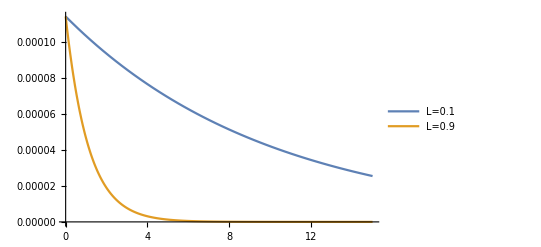

```mathematica
Plot[{S[n,0.1],S[n,0.9]},{n,0,15},PlotLegends->{"L=0.1","L=0.9"}]
```

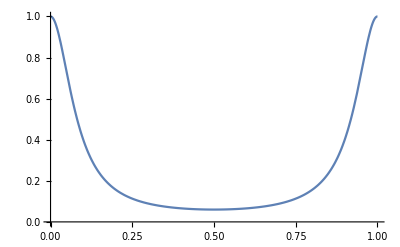

```mathematica
Plot[Cor[x,L]/σ^2,{x,0,1}]
```

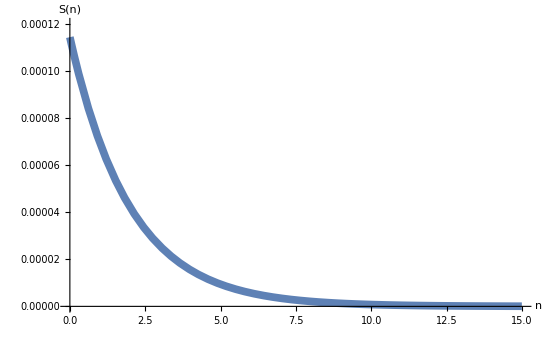

```mathematica
Plot[S[n,L],{n,0,15},PlotRange->{{0,15},{0,0.00012}},AxesLabel->{Style[n,Large],Style["S(n)",Large]},LabelStyle->Directive[Large, Black,Bold],PlotStyle->{Thickness[0.01]},AxesStyle->Thick]
```

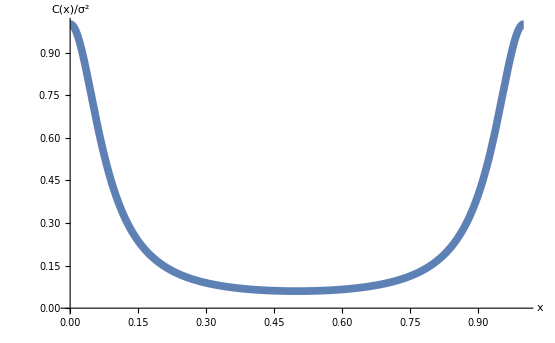

```mathematica
Plot[Cor[x,L]/σ^2,{x,0,1},PlotRange->{{0,1},{0,1}},AxesLabel->{Style[x,Large],Style["C(x)/σ^2",Large]},LabelStyle->Directive[Large, Black,Bold],PlotStyle->{Thickness[0.01]},AxesStyle->Thick]
```

```mathematica
tmp=Exp[(Log[4]+Log[3.56])/2];
```

```mathematica
N[Log[4]-Log[tmp]]
```

0.0582669

```mathematica
N[Log[tmp]-Log[3.56]]
```

0.0582669